```mathematica
V=(ћ^2*l*(l+1))/(2m*r^2)-(Z*e^2)/(4π*ϵ*r);
DSolve[{-𝔼*R[r]==(-(ћ^2)/(2m))*D[R[r],r,r]+V*R[r]},R,r]
```

{{R→Function[{r},C[1] WhittakerM[(e^2 √m Z)/(4 √2 ћ π √𝔼 ϵ),1/2 (1+2 l),(2 √2 √m r √𝔼)/ћ]+C[2] WhittakerW[(e^2 √m Z)/(4 √2 ћ π √𝔼 ϵ),1/2 (1+2 l),(2 √2 √m r √𝔼)/ћ]]}}

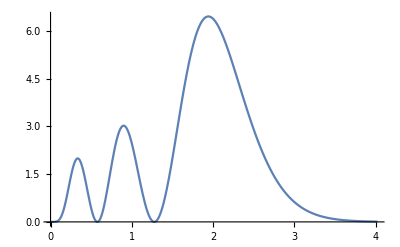

```mathematica
Z=1;
ћ=1.0545718*10^(-34);
e=1.60217662*10^(-19);
m=9.10938356*10^(-31);
ϵ=8.854187817*10^(-12);
𝔼=(m*e^4)/(32π^2*ϵ^2*ћ^2*n^2);
a=76*(4π*ϵ*ћ^2)/(m*e^2);

n=5;
l=2;

Plot[WhittakerM[(e^2 √m Z)/(4 √2 ћ π √𝔼 ϵ),1/2 (1+2 l),(2 √2 √m r √𝔼)/ћ]^2,{r,0,a},PlotRange->All,PlotPoints->150]
```